# Grammar-based genetic programming

```mathematica
Needs["AdvancedMapping`",FileNameJoin[{ParentDirectory@NotebookDirectory[],"Extra","AdvancedMapping.wl"}]]
```

## Grammar definition and parsing

### Trading grammar description and possible terminals set

```mathematica
GrammarPrettifyRule[rule_]:=Style[rule["From"],Bold]->ReplaceAll[rule["To"],{NonTerm[arg_]:>Style[arg,Bold],Term[arg_]:>Style[arg,Italic]}];
GrammarPrettify[grammar_]:=Column[Map[GrammarPrettifyRule,grammar]];
grammar = {
<|"From"->"cond","To"->{Term["logicOp"],NonTerm["cond"],NonTerm["cond"]},
"Value"->Term["logicOp"]["Value"][NonTerm["cond"]["Value"],NonTerm["cond"]["Value"]]|>,

<|"From"->"cond","To"->{Term["not"],NonTerm["cond"]},
"Value"->Not[NonTerm["cond"]["Value"]]|>,

<|"From"->"cond","To"->{Term["numOp"],NonTerm["priceQuant"],NonTerm["priceQuant"]},
"Value"->Term["numOp"]["Value"][NonTerm["priceQuant"]["Value"],NonTerm["priceQuant"]["Value"]]|>,

<|"From"->"cond","To"->{Term["numOp"],NonTerm["volumeQuant"],NonTerm["volumeQuant"]},
"Value"->Term["numOp"]["Value"][NonTerm["volumeQuant"]["Value"],NonTerm["volumeQuant"]["Value"]]|>,

<|"From"->"priceQuant","To"->{Term["factor"],NonTerm["priceExpression"]},
"Value"->Times[Term["factor"]["Value"],NonTerm["priceExpression"]["Value"]]|>,

<|"From"->"priceQuant","To"->{NonTerm["priceExpression"]},
"Value"->NonTerm["priceExpression"]["Value"]|>,

<|"From"->"volumeQuant","To"->{Term["volumeValue"]},
"Value"->Term["volumeValue"]["Value"]|>,

<|"From"->"volumeQuant","To"->{NonTerm["volumeExpression"]},
"Value"->NonTerm["volumeExpression"]["Value"]|>,

<|"From"->"priceExpression","To"->{Term["techInd"],Term["observable"],Term["window"]},
"Value"->Term["techInd"]["Value"][Term["observable"]["Value"],Term["window"]["Value"]]|>,

<|"From"->"priceExpression","To"->{Term["lag"],Term["observable"]},
"Value"->Prev[Term["observable"]["Value"],Term["lag"]["Value"]]|>,

<|"From"->"priceExpression","To"->{Term["observable"]},
"Value"->Term["observable"]["Value"]|>,

<|"From"->"volumeExpression","To"->{Term["lag"],Term["volume"]},
"Value"->Prev[Term["volume"]["Value"],Term["lag"]["Value"]]|>,

<|"From"->"volumeExpression","To"->{Term["volume"]},
"Value"->Term["volume"]["Value"]|>
};
terminalSet = {
Term["logicOp","And"],Term["logicOp","Or"],
Term["numOp","Greater"],Term["numOp","GreaterEqual"],Term["numOp","Less"],Term["numOp","LessEqual"],
Term["observable","Open"],Term["observable","Low"],Term["observable","High"],Term["observable","Close"],
Term["lag","1"],Term["lag","5"],Term["lag","10"],Term["lag","50"],
Term["window","10"],Term["window","20"],Term["window","30"],Term["window","40"],Term["window","50"],
Term["factor","0.5"],Term["factor","0.7"],Term["factor","0.9"],Term["factor","1.1"],Term["factor","1.3"],Term["factor","1.5"],
Term["techInd","SMA"],Term["techInd","EMA"],
Term["not","Not"],Term["volume","Volume"],
Term["volumeValue","5000"],Term["volumeValue","10000"],Term["volumeValue","50000"],Term["volumeValue","100000"],Term["volumeValue","500000"],Term["volumeValue","1000000"]
};
```

```mathematica
GrammarPrettify[grammar]
```

cond→{logicOp,cond,cond}
cond→{not,cond}
cond→{numOp,priceQuant,priceQuant}
cond→{numOp,volumeQuant,volumeQuant}
priceQuant→{factor,priceExpression}
priceQuant→{priceExpression}
volumeQuant→{volumeValue}
volumeQuant→{volumeExpression}
priceExpression→{techInd,observable,window}
priceExpression→{lag,observable}
priceExpression→{observable}
volumeExpression→{lag,volume}
volumeExpression→{volume}

```mathematica
GrammarGraph[grammar_]:=Block[{graphData,allSymbols,colorStyle},
graphData = DeleteDuplicates[Flatten[Map[Thread,Map[(NonTerm[#["From"]]->#["To"])&,grammar]]]];
allSymbols = DeleteDuplicates[Flatten[Map[{NonTerm[#["From"]],#["To"]}&,grammar]]];
colorStyle = Join[Thread[Cases[allSymbols,_NonTerm]->Blue],Thread[Cases[allSymbols,_Term]->Red]];

Graph[graphData,VertexLabels->"Name",VertexStyle->colorStyle,ImageSize->800]
];
```

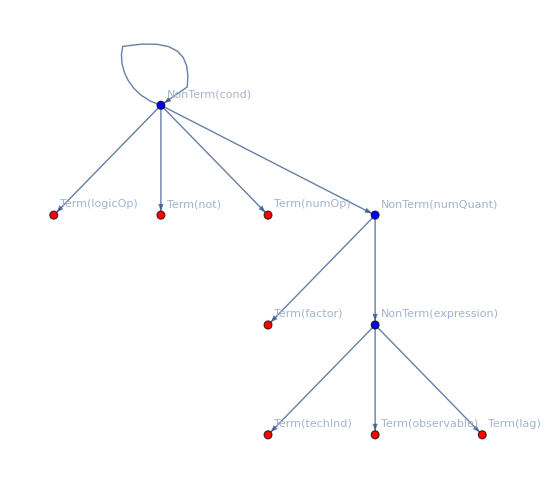

```mathematica
GrammarGraph[grammar]
```

### Expression tree synthesization

Separate head from arguments

```mathematica
GetComponents[expr_/;Depth[expr]<3]:={expr};
GetComponents[expr_/;Depth[expr]==3]:=Prepend[Level[expr,{1}],Head[expr]];
```

```mathematica
GetComponents[Less["Close",Prev[3,"Open"]]]
```

{Less,Close,Prev[3,Open]}

Rebuild expression from components

```mathematica
ExprFromComponents[components_ /;Length[components]≤1]:=First[components];
ExprFromComponents[components_ /;Length[components]>1]:=Block[{head,rest},
{head,rest} = {First[components],Rest[components]};
Apply[head,rest]
];
```

```mathematica
ExprFromComponents[{Less,"Close",Prev[3,"Open"]}] // FullForm
```

Less["Close",Prev[3,"Open"]]

Find the positions of values to be synthesized on the synthesizations list

```mathematica
GetValue[treeSymbol_,grammar_]:=ReplaceAll[treeSymbol,NonTerm[_,rule_]:>grammar[[rule]]["Value"]];
MatchPositions[expr_,synthesizations_]:=Block[{pos,newSynth,recursive},
pos = FirstPosition[synthesizations,First[expr]];
If[pos =!=Missing["NotFound"],
newSynth = ReplacePart[synthesizations,First[pos]->Found],
newSynth = synthesizations;
pos = {};
];
recursive = If[Rest[expr]≠{},MatchPositions[Rest[expr],newSynth],{}];
Transpose@{Flatten@Join[pos,recursive]}
];
```

```mathematica
synthValue = GetValue[NonTerm["expression",8],grammar]
```

Term[observable][Value]

```mathematica
MatchPositions[GetComponents[synthValue],{Term["observable"]["Value"],Term["numOp"]["Value"],Term["logicOp"]["Value"]}]
```

{{1}}

Synthesize the value of the current components from the list of synthValues.

```mathematica
Synthesize[exprComponents_,synthValues_]:=Block[{positions,lastPos,tmpSynthValues = synthValues,tmpExprComponents = exprComponents},
Do[
positions = Position[tmpSynthValues[[All,1]],tmpExprComponents[[i]]];
If[positions≠ {},
lastPos = First@Last@positions;
tmpExprComponents[[i]] = Replace[tmpExprComponents[[i]],Part[tmpSynthValues,lastPos]];
tmpSynthValues = Delete[tmpSynthValues,lastPos];
];
,{i,1,Length[tmpExprComponents]}
];
ExprFromComponents@tmpExprComponents
];
```

```mathematica
GetComponents[synthValue]
```

{Term[observable][Value]}

```mathematica
Synthesize[
GetComponents[synthValue],
Extract[{Term["observable"]["Value"]->"High",Term["numOp"]["Value"]->"Greater",Term["logicOp"]["Value"]->"And"},{{1}}]
]
```

High

Synthesize terminals and nonterminals.

```mathematica
SynthesizeNonTerm[treeSymbol_,grammar_,synthesizations_]:=Block[{val,components,eval,matchPos,newSynth,newSynthLabel},
val = GetValue[treeSymbol,grammar];
components = GetComponents[val];
matchPos = MatchPositions[components,synthesizations[[All,1]]];
eval = Synthesize[components,Extract[synthesizations,matchPos]];
newSynth = Delete[synthesizations,matchPos];
newSynthLabel = ReplaceAll[treeSymbol,NonTerm[x_,_]:>NonTerm[x]["Value"]];

Prepend[newSynth,newSynthLabel->eval]
];

SynthesizeTerm[treeSymbol_,synthesizations_]:=Block[{eval,new},
(* Label the value of a Terminal *)
If[Length[treeSymbol]==2,
Prepend[synthesizations, ReplaceAll[treeSymbol,Term[termName_,value_]:>(Term[termName]["Value"]->value)]],
synthesizations
]
];
```

```mathematica
SynthesizeNonTerm[NonTerm["expression",8],grammar,{Term["observable"]["Value"]->"High",Term["numOp"]["Value"]->"Greater",Term["logicOp"]["Value"]->"And"}]
```

{NonTerm[expression][Value]→High,Term[numOp][Value]→Greater,Term[logicOp][Value]→And}

```mathematica
SynthesizeTerm[Term["observable","High"],{Term["numOp"]["Value"]->"Greater",Term["logicOp"]["Value"]->"And"}]
```

{Term[observable][Value]→High,Term[numOp][Value]→Greater,Term[logicOp][Value]→And}

Complete tree synthesization.

```mathematica
SynthesizeTree[graph_,labels_,grammar_]:=Block[{depthFirstScan,labeledDFS,symbolType,synthesized},
(* Walk the parse tree in post order *)
depthFirstScan = First@Last@Reap[
DepthFirstScan[graph,1,{"PostvisitVertex"->(Sow[#]&)}]
];
labeledDFS = depthFirstScan /.labels;

(* Synthesize in the order of the depthfirstscan *)
synthesized={};
Do[
symbolType = Head[s];
If[symbolType === Term,synthesized = SynthesizeTerm[s,synthesized]];
If[symbolType === NonTerm,synthesized = SynthesizeNonTerm[s,grammar,synthesized]];
,
{s,labeledDFS}
];

ToExpression@ToString@Return[synthesized[[1,-1]]] /.{Open->"Open",High->"High",Low->"Low",Close->"Close",Volume->"Volume"}
];
```

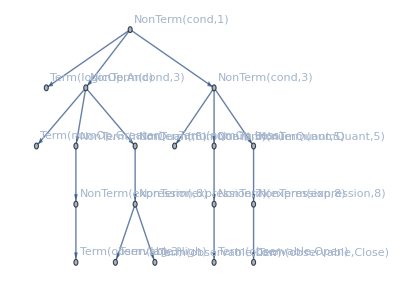

```mathematica
edgeList1 = {1->2,1->3,1->4,3->5,3->6,3->7,6->8,8->9,7->10,10->11,10->12,4->13,4->14,4->15,14->16,16->17,15->18,18->19};
labels1 = {1->NonTerm["cond",1],2->Term["logicOp","And"],3->NonTerm["cond",3],4->NonTerm["cond",3],5->Term["numOp","Greater"] ,6->NonTerm["numQuant",5] ,7->NonTerm["numQuant",5] ,8->NonTerm["expression",8] ,9->Term["observable","High"] ,10->NonTerm["expression",7] ,11->Term["lag","3"] ,12->Term["observable","Low"] ,13->Term["numOp","Less"] ,14->NonTerm["numQuant",5] ,15->NonTerm["numQuant",5] ,16->NonTerm["expression",8] ,17->Term["observable","Open"] ,18-> NonTerm["expression",8],19-> Term["observable","Close"]};
g1 = Graph[edgeList1,VertexLabels->labels1]
```

```mathematica
SynthesizeTree[g1,labels1,grammar] // FullForm
```

And[Greater["High",Prev["Low",3]],Less["Open","Close"]]

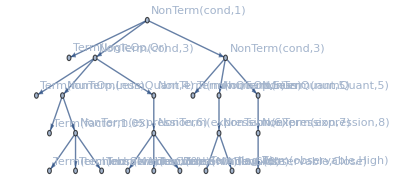

```mathematica
edgeList2 = {1->2,1->3,1->4,3->5,3->6,3->7,6->8,6->9,9->10,9->11,9->12,7->13,13->14,13->15,13->16,4->17,4->18,4->19,18->20,20->21,20->22,19->23,23->24};
labels2 = {1->NonTerm["cond",1],2->Term["logicOp","Or"],3->NonTerm["cond",3],4->NonTerm["cond",3],5-> Term["numOp","Less"],6->NonTerm["numQuant",4] ,7-> NonTerm["numQuant",5],8->Term["factor","1.05"] ,9->NonTerm["expression",6] ,10-> Term["techInd","SMA"],11-> Term["observable","Close"],12->Term["window","20"] ,13->NonTerm["expression",6] ,14->Term["techInd","SMA"] ,15->Term["observable","Close"] ,16->Term["window","40"] ,17->Term["numOp","Less"] ,18->NonTerm["numQuant",5] ,19->NonTerm["numQuant",5] ,20->NonTerm["expression",7],21->Term["lag","2"],22->Term["observable","Close"],23->NonTerm["expression",8],24->Term["observable","High"]};
g2 = Graph[edgeList2,VertexLabels->labels2]
```

```mathematica
SynthesizeTree[g2,labels2,grammar]//FullForm
```

Or[Less[Times[1.05,SMA["Close",20]],SMA["Close",40]],Less[Prev["Close",2],"High"]]

## Operations on trees

Tree manipulations operations.

```mathematica
RestartLabelsAt[graph_,labels_,startNum_ : 1]:=Block[{replaceRules,newEdges,newLabels},
replaceRules = Thread[VertexList[graph]->Range[startNum,startNum+Length[VertexList[graph]]-1]];
newEdges = EdgeList[graph]/.replaceRules;
newLabels = MapAt[#/.replaceRules&,labels,{All,1}];

{Graph[newEdges,VertexLabels->newLabels],newLabels}
];
Subtree[graph_,labels_,vertex_]:=Block[{children,toDelete,subtree,sublabels},
children = First@Last@Reap@DepthFirstScan[graph,vertex,{"PrevisitVertex"->(Sow[#]&)}];
toDelete = Complement[VertexList[graph],children];
subtree = VertexDelete[graph,Complement[VertexList[graph],children]];
sublabels = Cases[labels,x_/;MemberQ[children,First[x]]];

{subtree,sublabels}
];
DeleteSubtree[graph_,labels_,vertex_]:=Block[{subtree,sublabels,subVertexes,conectionRemoved,withoutSubtree,newLabels},
{subtree,sublabels} = Subtree[graph, labels, vertex];
subVertexes = VertexList[subtree];
conectionRemoved = ReplaceAll[EdgeList[graph],((x_/;!MemberQ[subVertexes,x])->(y_/;MemberQ[subVertexes,y])):>x->Empty];
withoutSubtree = If[Length[Intersection[VertexList[conectionRemoved],subVertexes]]≠ 0,
VertexDelete[conectionRemoved,subVertexes],
conectionRemoved
];
newLabels = Complement[labels,sublabels];

{Graph[withoutSubtree,VertexLabels->newLabels],newLabels}
];

InsertSubtree[graph_,labels_,subtree_,sublabels_]:=Block[{missingVertexes,edges,missing,splitPos,left,right,middleRules,formattedSubtreeRoot,remaining,rightRules,newLeftGraph,newMiddleGraph,newRightGraph,insertLabels,incompleteLabels,newEdges,newLabels,newRootForSub,newRightLabels},
If[!MemberQ[VertexList[graph],Empty],Return[$Failed]];

edges = DeleteCases[VertexList[graph],Empty];
missingVertexes = Complement[Range[Max[edges]],edges];
If[missingVertexes ≠ {},
missing =  First@missingVertexes;
splitPos = First@FirstPosition[EdgeList[graph],_->Empty];
{left,right} = TakeDrop[EdgeList[graph],splitPos];

middleRules = Thread[VertexList[subtree]->(VertexList[subtree]+missing-1)];
newMiddleGraph = EdgeList[subtree]/.middleRules;
formattedSubtreeRoot = 1 /.middleRules;

remaining = Complement[VertexList[right],VertexList[left]];
rightRules = Thread[remaining->(remaining+Max[VertexList[newMiddleGraph]]-Min[remaining]+1)];

newLeftGraph = left/.Empty->formattedSubtreeRoot;
newRightGraph = right /.rightRules;
insertLabels = MapAt[#/.middleRules&,sublabels,{All,1}];
incompleteLabels = MapAt[#/.rightRules&,labels,{All,1}];

newEdges = Join[newLeftGraph,newMiddleGraph,newRightGraph];
newLabels = SortBy[Join[incompleteLabels,insertLabels],First];

,

newRootForSub = Max[DeleteCases[VertexList[graph],Empty]]+1;
{newRightGraph,newRightLabels} = RestartLabelsAt[subtree,sublabels,newRootForSub];
newEdges = Join[EdgeList[graph]/.Empty->newRootForSub,EdgeList[newRightGraph]];
newLabels = Join[labels,newRightLabels];
];

{Graph[newEdges,VertexLabels->newLabels],newLabels}
];
```

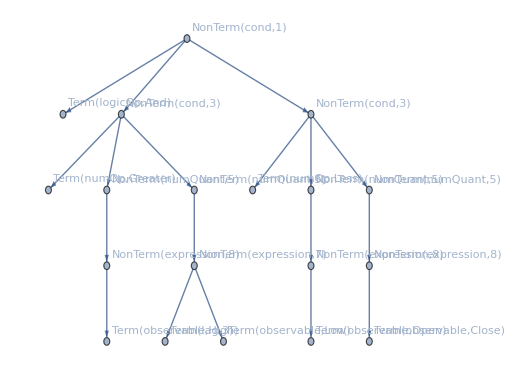

```mathematica
g1
```

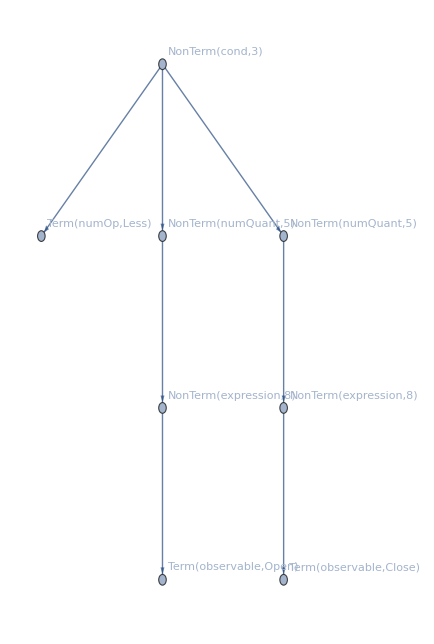
{-Graphics-,{1→NonTerm[cond,3],2→Term[numOp,Less],3→NonTerm[numQuant,5],4→NonTerm[numQuant,5],5→NonTerm[expression,8],6→Term[observable,Open],7→NonTerm[expression,8],8→Term[observable,Close]}}

```mathematica
subtree1 = Apply[RestartLabelsAtOne,Subtree[g1,labels1,4]]
```

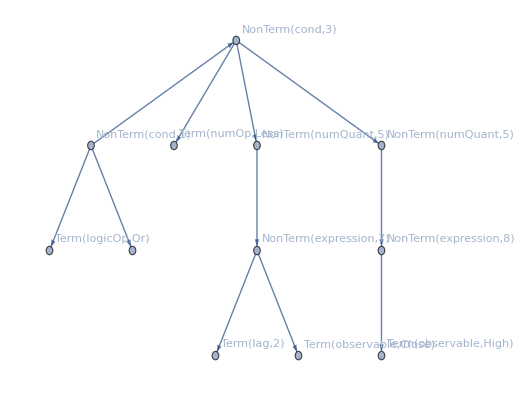
{-Graphics-,{1→NonTerm[cond,1],2→Term[logicOp,Or],4→NonTerm[cond,3],17→Term[numOp,Less],18→NonTerm[numQuant,5],19→NonTerm[numQuant,5],20→NonTerm[expression,7],21→Term[lag,2],22→Term[observable,Close],23→NonTerm[expression,8],24→Term[observable,High]}}

```mathematica
cropped2 = DeleteSubtree[g2,labels2,3]
```

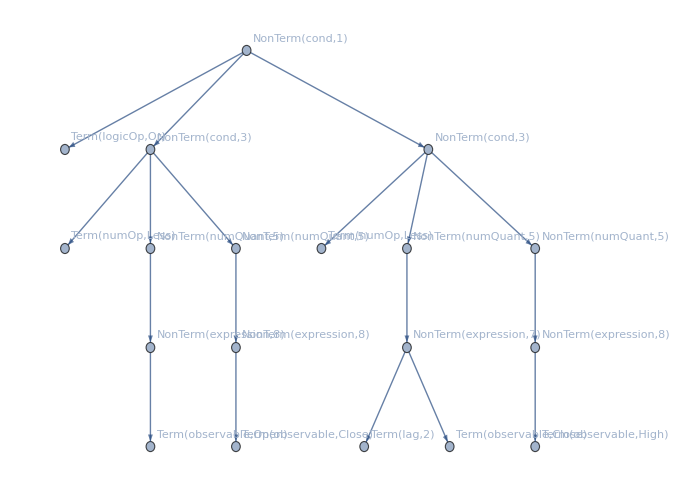
{-Graphics-,{1→NonTerm[cond,1],2→Term[logicOp,Or],3→NonTerm[cond,3],4→Term[numOp,Less],5→NonTerm[numQuant,5],6→NonTerm[numQuant,5],7→NonTerm[expression,8],8→Term[observable,Open],9→NonTerm[expression,8],10→Term[observable,Close],19→NonTerm[cond,3],32→Term[numOp,Less],33→NonTerm[numQuant,5],34→NonTerm[numQuant,5],35→NonTerm[expression,7],36→Term[lag,2],37→Term[observable,Close],38→NonTerm[expression,8],39→Term[observable,High]}}

```mathematica
inserted = InsertSubtree[First[cropped2],Last[cropped2],First[subtree1],Last[subtree1]]
```

```mathematica
SynthesizeTree[First[inserted],Last[inserted],grammar] // FullForm
```

Or[Less["Open","Close"],Less[Prev["Close",2],"High"]]

## Crossover

Crossover operator that selects NonTerms that are common in both parents and swaps them.

```mathematica
Crossover[graph1_,labels1_,graph2_,labels2_]:=Block[{nonterms1,nonterms2,commonNonTerms,matchsIn1,vertex1,vertex1NonTerm,vertex2,cropped,sub},
nonterms1 = Cases[labels1[[All,2]],_NonTerm];
nonterms2 = Cases[labels2[[All,2]],_NonTerm];
commonNonTerms = Intersection[nonterms1,nonterms2];

matchsIn1 = Cases[labels1,HoldPattern[v_->l_/;MemberQ[commonNonTerms,l]]:>{v,l}];
If[Length[matchsIn1]<2,Return[RandomChoice[{{graph1,labels1},{graph2,labels2}}]]];

{vertex1,vertex1NonTerm} = RandomChoice[Drop[matchsIn1,1]];
vertex2 = RandomChoice[Cases[labels2,HoldPattern[v_->l_/;l==vertex1NonTerm]:>v]];
cropped = DeleteSubtree[graph1,labels1,vertex1];
sub = Apply[RestartLabelsAt,Subtree[graph2,labels2,vertex2]];

InsertSubtree[First[cropped],Last[cropped],First[sub],Last[sub]]
];
PopulationCrossover[population_,childrenPerCouple_]:=Block[{parts},
parts = Partition[RandomSample[population],2];
Apply[Join,Table[Map[Apply[Crossover,Flatten[#,1]]&,parts],childrenPerCouple]]
];
```

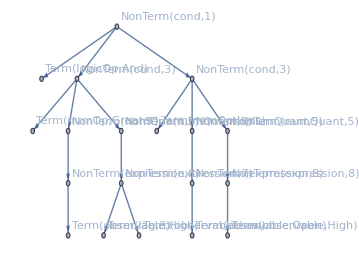
{-Graphics-,{1→NonTerm[cond,1],2→Term[logicOp,And],3→NonTerm[cond,3],4→NonTerm[cond,3],5→Term[numOp,Greater],6→NonTerm[numQuant,5],7→NonTerm[numQuant,5],8→NonTerm[expression,8],9→Term[observable,High],10→NonTerm[expression,7],11→Term[lag,3],12→Term[observable,Low],13→Term[numOp,Less],14→NonTerm[numQuant,5],15→NonTerm[numQuant,5],16→NonTerm[expression,8],17→Term[observable,Open],18→NonTerm[expression,8],19→Term[observable,High]}}

```mathematica
{crossoverTree,crossoverLabels} = Crossover[g1,labels1,g2,labels2]
```

```mathematica
SynthesizeTree[crossoverTree,crossoverLabels,grammar]// FullForm
```

And[Greater["High",Prev["Low",3]],Less["Open","Close"]]

## Mutation

```mathematica
TreeMutation[graph_,labels_]:=Crossover[graph,labels,graph,labels];
TerminalMutation[labels_,terminalSet_]:=Block[{choice,type,newTerm,availableTerms},
choice = RandomChoice[Cases[labels,HoldPattern[_->_Term]]];
type = First[Level[Last[choice],{1}]];
availableTerms = Complement[Cases[terminalSet,Term[type,_]],{Last[choice]}];

If[availableTerms ≠ {},
newTerm = RandomChoice[availableTerms];
ReplacePart[labels,First[choice]->(First[choice]->newTerm)]
,
labels
]
];
Mutation[graph_,labels_,terminalSet_]:=Block[{mutatedSymbols},
If[RandomReal[]≥0.5,
TreeMutation[graph,labels],
mutatedSymbols = TerminalMutation[labels,terminalSet];
{Graph[EdgeList[graph],VertexLabels->mutatedSymbols],mutatedSymbols}
]
];
PopulationMutate[population_,probability_,terminalSet_]:=Map[If[RandomReal[]≤probability,Mutation[First[#],Last[#],terminalSet],#]&,population];
```

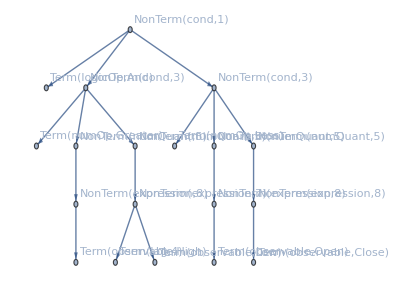
{-Graphics-,{1→NonTerm[cond,1],2→Term[logicOp,And],3→NonTerm[cond,3],4→NonTerm[cond,3],5→Term[numOp,Greater],6→NonTerm[numQuant,5],7→NonTerm[numQuant,5],8→NonTerm[expression,8],9→Term[observable,High],10→NonTerm[expression,7],11→Term[lag,4],12→Term[observable,Low],13→Term[numOp,Less],14→NonTerm[numQuant,5],15→NonTerm[numQuant,5],16→NonTerm[expression,8],17→Term[observable,Open],18→NonTerm[expression,8],19→Term[observable,Close]}}

```mathematica
{mutatedTree,mutatedLabels} = Mutation[g1,labels1,terminalSet]
```

```mathematica
SynthesizeTree[mutatedTree,mutatedLabels,grammar]
```

High>Prev[Low,4]&&Open<Close

## Fitness function

### Database creation

```mathematica
dateFolders = Select[FileNames["*",FileNameJoin[{ParentDirectory@NotebookDirectory[],"Datasets","BMV"}]],FileExtension[#]==""&];
```

```mathematica
dates = Map[FileBaseName,dateFolders]
```

{2020-01-20,2020-01-21,2020-01-22,2020-01-23,2020-01-24,2020-01-27,2020-01-28,2020-01-29,2020-01-30,2020-01-31,2020-02-04,2020-02-05,2020-02-06,2020-02-07,2020-02-10,2020-02-11,2020-02-12,2020-02-13,2020-02-14}

```mathematica
{trainingDates,validationDates} = TakeDrop[dates,Ceiling[0.8Length[dates]]];
```

```mathematica
stockPaths = FileNames["*",FileNameJoin[{ParentDirectory@NotebookDirectory[],"Datasets","BMV",First[dates]}]];
stocks = Map[FileBaseName,stockPaths]
```

{AC.MX,ALPEKA.MX,ALSEA.MX,AMXL.MX,ASURB.MX,BBAJIOO.MX,BIMBOA.MX,BOLSAA.MX,BSMXB.MX,CEMEXCPO.MX,CUERVO.MX,GAPB.MX,GCARSOA1.MX,GCC.MX,GENTERA.MX,GFNORTEO.MX,GMEXICOB.MX,GRUMAB.MX,IENOVA.MX,KIMBERA.MX,KOFUBL.MX,LABB.MX,LIVEPOLC-1.MX,MEGACPO.MX,OMAB.MX,ORBIA.MX,PE&OLES.MX,PINFRA.MX,RA.MX,TLEVISACPO.MX}

```mathematica
AdaptativeMovingAverage[maFunc_,list_,r_]:=Join[Table[First@maFunc[Take[list,n],n],{n,1,r-1}],maFunc[list,r]];
LaggedList[list_,lag_]:=Join[ConstantArray[First[list],lag],Drop[list,-lag]];

BuildDerivatives[dataset_]:=Block[{keys,windows,obsWindowTuples,sma,ema,lags,obsLagTuples,prev,derivatives,derivativesData},
keys = Keys[First[dataset]];
windows = Cases[terminalSet,Term["window",l_]:>ToExpression[l]];
obsWindowTuples = Tuples[{keys,windows}];
lags = Cases[terminalSet,Term["lag",l_]:>ToExpression[l]];
obsLagTuples = Tuples[{keys,lags}];

sma =Map[Apply[SMA,#]->AdaptativeMovingAverage[MovingAverage,dataset[[All,First[#]]],Last[#]]&,obsWindowTuples];
ema =Map[Apply[EMA,#]->ExponentialMovingAverage[dataset[[All,First[#]]],Last[#]/100]&,obsWindowTuples];
prev = Map[Apply[Prev,#]->LaggedList[dataset[[All,First[#]]],Last[#]]&,obsLagTuples];
derivatives = Map[Thread,Join[sma,ema,prev]];
derivativesData = Map[Association,Transpose[derivatives]];

MapThread[Join,{derivativesData,dataset}]

];
```

```mathematica
CreateTick[{open_,high_,low_,close_,volume_}]:=<|"Open"->open,"High"->high,"Low"->low,"Close"->close,"Volume"->volume|>;
CreateTickDatabase[date_,stock_]:=Block[{path,dataset},
path = FileNameJoin[{ParentDirectory@NotebookDirectory[],"Datasets","BMV",date}];
dataset = DeleteCases[Import[FileNameJoin[{path,StringJoin[stock,".csv"]}]],{_,"","","","",""}];

BuildDerivatives@Map[CreateTick[Drop[#,1]]&,Drop[dataset,1]]
];
CreateMarketDailyDatabase[date_,stocks_]:=Association[ProgressMap[#->CreateTickDatabase[date,#]&,stocks]];
```

```mathematica
databaseFile = FileNameJoin[{NotebookDirectory[],"gp_database.mx"}];
If[FileExistsQ[databaseFile],
stockDatabase = Import[databaseFile],

stockDatabase = ProgressMap[CreateMarketDailyDatabase[#,stocks]&,dates];
Export[databaseFile,stockDatabase];
];
```

### Backtesting implementation

```mathematica
StrategyValues[strategyFunc_,tradingDayData_]:=Map[ReplaceAll[strategyFunc,#]&,tradingDayData];
StrategySignals[strategyFunc_,tradingDayData_]:=Block[{strategyValues,signals},
strategyValues = Join[Drop[StrategyValues[strategyFunc,tradingDayData],-2],{False,False}]; (* Always sell at the end *)
signals = Flatten[Map[
Join[
{First[#]/.{True->"Enter",False->"Exit"}},
ConstantArray["Hold",Length[#]-1]
]&,Split[strategyValues]
]
];

If[First[signals]=="Exit",ReplacePart[signals,1->"Hold"],signals]
];
StrategyReturn[strategyFunc_,tradingDayData_,transactionCost_]:=Block[{signals,enterPositions,exitPositions,buyPrices,sellPrices},
signals = StrategySignals[strategyFunc,tradingDayData];
enterPositions = Position[Drop[signals,-2],"Enter"]+1;
exitPositions = Position[Drop[signals,-2],"Exit"]+1;
If[enterPositions=={} || exitPositions == 0,Return[0.0]];

buyPrices = Extract[tradingDayData,enterPositions][[All,"Open"]];
sellPrices = Extract[tradingDayData,exitPositions][[All,"Open"]];

Total[Log[sellPrices(1-transactionCost)]]-Total[Log[buyPrices(1+transactionCost)]]
];
StrategyPerformanceOverTime[strategyFunc_,tradingDayData_,transactionCost_]:=Block[{signals,balance,laggedSignals},
signals = StrategySignals[strategyFunc,tradingDayData];
balance = 0;
laggedSignals = Prepend[Drop[signals,-1],Last[signals]];

Table[
If[laggedSignals[[i]]=="Enter",balance -= tradingDayData[[i]]["Open"]*(1+transactionCost)];
If[laggedSignals[[i]]=="Exit",balance += tradingDayData[[i]]["Open"]*(1-transactionCost)];
balance
,{i,1,Length[tradingDayData]}
]
];
```

```mathematica
strategyFunc = Or[Less[Times[1.05,SMA["Close",20]],SMA["Close",40]],Less[Prev["Close",2],"High"]];
```

```mathematica
tradingDayData = stockDatabase[[1,"AC.MX"]];
```

```mathematica
StrategyValues[strategyFunc,tradingDayData]
```

{True,True,True,False,False,True,True,True,False,False,True,True,True,True,False,False,False,True,False,False,False,False,True,True,True,False,True,True,False,False,False,False,True,True,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,False,True,True,False,False,True,False,True,True,True,False,False,False,True,True,True,False,False,False,False,False,True,True,True,False,False,False,False,False,False,False,False,True,True,True,False,True,True,False,False,False,False,False,False,True,True,False,True,False,False,True,False,False,False,False,True,True,False,False,True,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,True,True,False,False,False,True,True,True,True,False,False,False,False,False,False,False,True,True,True,False,False,False,False,False,False,False,False,False,False,True,False,True,True,True,True,True,True,True,True}

```mathematica
signals = StrategySignals[strategyFunc,tradingDayData]
```

{Enter,Hold,Hold,Exit,Hold,Enter,Hold,Hold,Exit,Hold,Enter,Hold,Hold,Hold,Exit,Hold,Hold,Enter,Exit,Hold,Hold,Hold,Enter,Hold,Hold,Exit,Enter,Hold,Exit,Hold,Hold,Hold,Enter,Hold,Exit,Hold,Hold,Hold,Enter,Exit,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Enter,Hold,Exit,Hold,Hold,Hold,Enter,Hold,Exit,Hold,Enter,Exit,Enter,Hold,Hold,Exit,Hold,Hold,Enter,Hold,Hold,Exit,Hold,Hold,Hold,Hold,Enter,Hold,Hold,Exit,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Enter,Hold,Hold,Exit,Enter,Hold,Exit,Hold,Hold,Hold,Hold,Hold,Enter,Hold,Exit,Enter,Exit,Hold,Enter,Exit,Hold,Hold,Hold,Enter,Hold,Exit,Hold,Enter,Hold,Exit,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Enter,Hold,Exit,Hold,Hold,Enter,Hold,Hold,Hold,Exit,Hold,Hold,Hold,Hold,Hold,Hold,Enter,Hold,Hold,Exit,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Hold,Enter,Exit,Enter,Hold,Hold,Hold,Hold,Hold,Exit,Hold}

```mathematica
StrategyReturn[strategyFunc,tradingDayData,0.0025]
```

-4.79954

### Population evaluation

```mathematica
EvaluatePopulation[population_,trainingDates_,transactionCost_,bloatControl_ :0.0]:=Block[{stock,date,tradingDayData,populationAsFunctions},
stock = RandomChoice[stocks];
date = RandomInteger[{1,Length[trainingDates]}];
tradingDayData = stockDatabase[[date,stock]];
populationAsFunctions = Map[SynthesizeTree[First[#],Last[#],grammar]&,population];

MapThread[
<|
"Genome"->#1,
"Score"->Ramp[StrategyReturn[#2,tradingDayData,transactionCost]]-bloatControl*LeafCount[#2]
|>&,
{population,populationAsFunctions}
]
];
```

```mathematica
population = {{g1,labels1},{g2,labels2}};
```

```mathematica
EvaluatePopulation[population,trainingDates,0.0025]
```

{<|Genome→{-Graphics-,{1→NonTerm[cond,1],2→Term[logicOp,And],3→NonTerm[cond,3],4→NonTerm[cond,3],5→Term[numOp,Greater],6→NonTerm[numQuant,5],7→NonTerm[numQuant,5],8→NonTerm[expression,8],9→Term[observable,High],10→NonTerm[expression,7],11→Term[lag,3],12→Term[observable,Low],13→Term[numOp,Less],14→NonTerm[numQuant,5],15→NonTerm[numQuant,5],16→NonTerm[expression,8],17→Term[observable,Open],18→NonTerm[expression,8],19→Term[observable,Close]}},Return→3.23633|>,<|Genome→{-Graphics-,{1→NonTerm[cond,1],2→Term[logicOp,Or],3→NonTerm[cond,3],4→NonTerm[cond,3],5→Term[numOp,Less],6→NonTerm[numQuant,4],7→NonTerm[numQuant,5],8→Term[factor,1.05],9→NonTerm[expression,6],10→Term[techInd,SMA],11→Term[observable,Close],12→Term[window,20],13→NonTerm[expression,6],14→Term[techInd,SMA],15→Term[observable,Close],16→Term[window,40],17→Term[numOp,Less],18→NonTerm[numQuant,5],19→NonTerm[numQuant,5],20→NonTerm[expression,7],21→Term[lag,2],22→Term[observable,Close],23→NonTerm[expression,8],24→Term[observable,High]}},Return→-0.352468|>}

## Population initialization

```mathematica
NonTermName[nonterm_]:=ReplaceAll[nonterm,NonTerm[x_]:>x];
NonTermWithProd[nonterm_,prodIndex_]:=NonTerm[NonTermName[nonterm],prodIndex];
ApplicableProductions[nonterm_,grammar_]:=First@Transpose@Position[grammar,KeyValuePattern["From"->NonTermName[nonterm]]];
UnassignedProductionQ[prod_]:=MatchQ[prod,NonTerm[_]];

ProductionRuleAsGraph[grammar_,prodIndex_]:=Block[{rootNonTerm,newLeafs,edgeList,vertexLabels},
rootNonTerm = NonTermWithProd[NonTerm[grammar[[prodIndex]]["From"]],prodIndex];
newLeafs = grammar[[prodIndex]]["To"];
edgeList = Thread[1->Range[2,1+Length[newLeafs]]];
vertexLabels = Prepend[Thread[Range[2,1+Length[newLeafs]]->newLeafs],1->rootNonTerm];

{Graph[edgeList,VertexLabels->vertexLabels],vertexLabels}
];

GrowTree[graph_,labels_,grammar_,maxDepth_]:=Block[{unassignedVertexes,replaceIndex,cropped,replaceNonTerm,selectedProduction,sub,new},
If[graph===$Failed || labels ===$Failed,Return[{$Failed,$Failed}]];

unassignedVertexes = Cases[labels,HoldPattern[v_->t_ /; UnassignedProductionQ[t]]:>v];
replaceIndex = RandomChoice[unassignedVertexes];
cropped = DeleteSubtree[graph,labels,replaceIndex];
replaceNonTerm = Last[labels[[replaceIndex]]];
selectedProduction = RandomChoice[ApplicableProductions[replaceNonTerm,grammar]];
sub = ProductionRuleAsGraph[grammar,selectedProduction];
new = InsertSubtree[First[cropped],Last[cropped],First[sub],Last[sub]];

If[Length[Last[new]]<100,new,{$Failed,$Failed}]
];

GenerateRandomTree[grammar_,maxDepth_]:=Block[{tree},
tree =ProductionRuleAsGraph[grammar,RandomInteger[{1,3}]];
NestWhile[
GrowTree[First[#],Last[#],grammar,maxDepth]&,tree,#=!={$Failed,$Failed}&&Apply[Or,Map[UnassignedProductionQ,Cases[Last[#][[All,2]],_NonTerm]]]&
]
];
RandomTerm[name_,terminalSet_]:=RandomChoice[Cases[terminalSet,Term[name,_]]];
GenerateRandomTerminals[labels_,terminalSet_]:=ReplaceAll[labels,HoldPattern[v_->Term[n_]]:>(v->RandomTerm[n,terminalSet])];

GenerateRandomFunction[grammar_,terminalSet_,maxDepth_]:=Block[{g=$Failed,l=$Failed,labelsWithTerminals},
While[g===$Failed || l ===$Failed,
{g,l} = GenerateRandomTree[grammar,maxDepth];
];
labelsWithTerminals = GenerateRandomTerminals[l,terminalSet];

{Graph[EdgeList[g],VertexLabels->labelsWithTerminals],labelsWithTerminals}
];
```

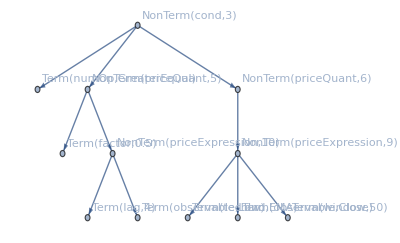
{-Graphics-,{1→NonTerm[cond,3],2→Term[numOp,GreaterEqual],3→NonTerm[priceQuant,5],4→Term[factor,0.5],5→NonTerm[priceExpression,10],6→Term[lag,4],7→Term[observable,Low],8→NonTerm[priceQuant,6],9→NonTerm[priceExpression,9],10→Term[techInd,EMA],11→Term[observable,Close],12→Term[window,50]}}

GreaterEqual[Times[0.5,Prev["Low",4]],EMA["Close",50]]

```mathematica
{g,l} = GenerateRandomFunction[grammar,terminalSet,100]
SynthesizeTree[g,l,grammar] // FullForm
```

```mathematica
GenerateInitialPopulation[size_,maxDepth_,trainingDates_,transactionCost_,bloatControl_]:=Block[{seeds,population},
population = Table[GenerateRandomFunction[grammar,terminalSet,maxDepth],size];

EvaluatePopulation[population,trainingDates,transactionCost,bloatControl]
];
```

```mathematica
population = GenerateInitialPopulation[10,trainingDates,0.0025];
```

## Selection

```mathematica
ProportionateSelectionIndexes[population_,n_]:=RandomSample[Reverse[Range[population]]->Range[population],n];

ProportionateRankedSelection[evaluatedGenome_,n_]:= Part[Reverse@SortBy[evaluatedGenome,Key["Score"]],ProportionateSelectionIndexes[Length[evaluatedGenome],n]];
```

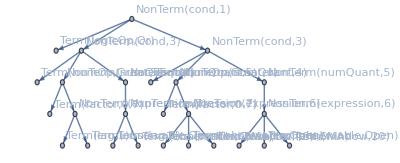
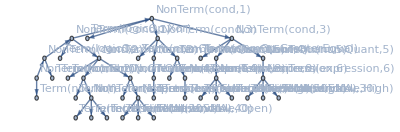
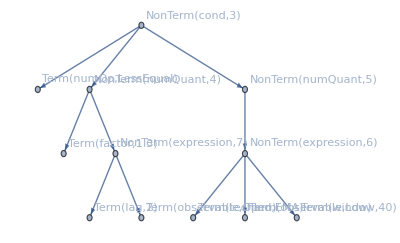
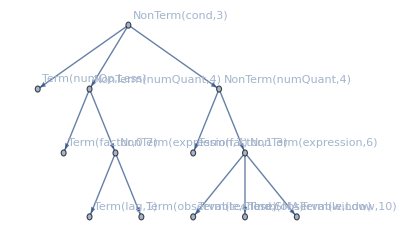
{<|Genome→{-Graphics-,{1→NonTerm[cond,1],2→Term[logicOp,Or],3→NonTerm[cond,3],4→NonTerm[cond,3],5→Term[numOp,GreaterEqual],6→NonTerm[numQuant,4],7→NonTerm[numQuant,5],8→NonTerm[expression,7],9→Term[lag,2],10→Term[observable,Close],11→Term[factor,0.7],12→NonTerm[expression,7],13→Term[lag,1],14→Term[observable,Open],15→Term[numOp,Greater],16→NonTerm[numQuant,4],17→NonTerm[numQuant,5],18→Term[factor,0.7],19→NonTerm[expression,6],20→Term[techInd,EMA],21→Term[observable,Open],22→Term[window,40],23→NonTerm[expression,6],24→Term[techInd,SMA],25→Term[observable,Open],26→Term[window,20]}},Return→5.32455|>,<|Genome→{-Graphics-,{1→NonTerm[cond,2],2→Term[not,Not],3→NonTerm[cond,2],4→Term[not,Not],5→NonTerm[cond,1],6→Term[logicOp,Xor],7→NonTerm[cond,1],8→NonTerm[cond,3],9→Term[logicOp,Xor],10→NonTerm[cond,3],11→NonTerm[cond,3],12→Term[numOp,Less],13→NonTerm[numQuant,5],14→NonTerm[numQuant,4],15→NonTerm[expression,8],16→Term[numOp,GreaterEqual],17→NonTerm[numQuant,5],18→NonTerm[numQuant,5],19→NonTerm[expression,6],20→Term[observable,Close],21→NonTerm[expression,6],22→Term[techInd,EMA],23→Term[observable,High],24→Term[window,30],25→Term[techInd,SMA],26→Term[observable,High],27→Term[window,50],28→Term[numOp,Greater],29→NonTerm[numQuant,4],30→NonTerm[numQuant,4],31→Term[factor,0.9],32→NonTerm[expression,8],33→Term[observable,High],34→Term[factor,1.1],35→NonTerm[expression,6],36→Term[factor,1.3],37→NonTerm[expression,6],38→Term[techInd,EMA],39→Term[observable,Low],40→Term[window,20],41→Term[techInd,SMA],42→Term[observable,Open],43→Term[window,40]}},Return→-0.0824303|>,<|Genome→{-Graphics-,{1→NonTerm[cond,3],2→Term[numOp,LessEqual],3→NonTerm[numQuant,4],4→NonTerm[numQuant,5],5→NonTerm[expression,6],6→Term[techInd,EMA],7→Term[observable,Low],8→Term[window,40],9→Term[factor,1.3],10→NonTerm[expression,7],11→Term[lag,2],12→Term[observable,Open]}},Return→5.32455|>,<|Genome→{-Graphics-,{1→NonTerm[cond,3],2→Term[numOp,Less],3→NonTerm[numQuant,4],4→NonTerm[numQuant,4],5→Term[factor,0.7],6→NonTerm[expression,7],7→Term[factor,1.3],8→NonTerm[expression,6],9→Term[lag,1],10→Term[observable,Close],11→Term[techInd,SMA],12→Term[observable,Low],13→Term[window,10]}},Return→-5.32955|>}

```mathematica
selected = ProportionateRankedSelection[population,4]
```

## Main algorithm

```mathematica
Generation[population_,survivors_,mutationProb_,elitism_,newBloodIndividuals_,trainingDates_,transactionCost_,bloatControl_]:=Block[{evaluated,fittest,newGeneration,mutated,childrenPerCouple,elite,sortedWithElite,newBlood,evaluatedElite,expressions,badExpressions},
fittest = ProportionateRankedSelection[population,survivors];
childrenPerCouple = (2 Length[population])/survivors;
newGeneration = PopulationCrossover[fittest[[All,"Genome"]],childrenPerCouple];
mutated = PopulationMutate[newGeneration,mutationProb,terminalSet];
evaluated = SortBy[EvaluatePopulation[mutated,trainingDates,transactionCost,bloatControl],Key["Score"]];
elite = Take[Reverse@SortBy[population,Key["Score"]],elitism][[All,"Genome"]];
evaluatedElite = EvaluatePopulation[elite,trainingDates,transactionCost,bloatControl];
sortedWithElite = Reverse@SortBy[Join[evaluatedElite,Drop[evaluated,elitism]],Key["Score"]];

expressions = Map[SynthesizeTree[First[#["Genome"]],Last[#["Genome"]],grammar]&,sortedWithElite];
badExpressions = Position[expressions,True|False];
sortedWithElite = Delete[sortedWithElite,badExpressions];

newBlood = GenerateInitialPopulation[newBloodIndividuals+Length[badExpressions],100,trainingDates,transactionCost,bloatControl];

Reverse@SortBy[Join[Drop[sortedWithElite,-newBloodIndividuals],newBlood],Key["Score"]]
];
EvolvePopulation[population_,survivors_,mutationProb_,elitism_,newBloodIndividuals_,trainingDates_,transactionCost_,bloatControl_,generations_]:=
ProgressNestList[
Generation[#,survivors,mutationProb,elitism,newBloodIndividuals,trainingDates,transactionCost,bloatControl]&,
population,generations,
"Label"->"Generation"
];
```

```mathematica
population = GenerateInitialPopulation[200,100,trainingDates,0.0025,0.005];
```

```mathematica
evolved = EvolvePopulation[population,50,0.5,2,trainingDates,0.0025,0.005,30];
```

$Aborted

```mathematica
evaluatedOnValidation = ProgressTable[Reverse@SortBy[EvaluatePopulation[evolved[[i]][[All,"Genome"]],validationDates,0.0025],Key["Score"]],{i,1,Length[evolved]}];
```

```mathematica
trainingScoreVsIter = Table[{k,Mean[evolved[[k]][[All,"Score"]]]},{k,1,Length[evolved]}];
validationScoreVsIter = Table[{k,Mean[evaluatedOnValidation[[k]][[All,"Score"]]]},{k,1,Length[evaluatedOnValidation]}];

ListLinePlot[
{trainingScoreVsIter,validationScoreVsIter},
PlotTheme->"Monochrome",
FrameLabel->{Style["k",15], Style["Average Score",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->Automatic,
Joined->{True,True},
PlotStyle->{RGBColor[0.689993, 0.089999, 0.119999],RGBColor[0.09, 0.3, 0.]},
Frame->True,
ImageSize->500,
PlotLegends->{"Training set","Validation set"}
]
```

### Interactive

```mathematica
GetSeconds[time_] := IntegerString[Round[Mod[time, 60]], 10, 2];
GetMinutes[time_]:= IntegerString[Mod[Floor[time/60], 60], 10, 2];
GetHours[time_] := IntegerString[Floor[time/3600], 10, 2];
ClockFormat[time_] := StringJoin[GetHours[time], ":", GetMinutes[time], ":", GetSeconds[time]];

ProgressEvolveIndicator[indexProgress_,totalSize_,startTime_,fittestIndPlot_,scorePlot_,scoresHistogram_]:=Block[{progressString,remainingTime,remainingTimeString,indicator,ellapsedTimeString},
progressString = Row[{Style["Progress: ",Bold],ToString[indexProgress],"/",ToString[totalSize]}];
ellapsedTimeString = Row[{Style["Ellapsed time: ",Bold],ClockFormat[AbsoluteTime[]-startTime]}];

If[indexProgress ≠ 0,
remainingTime = (AbsoluteTime[]-startTime)/indexProgress(totalSize-indexProgress);
remainingTimeString = Row[{Style["Remaining: ",Bold],ClockFormat[remainingTime]}];
,
remainingTimeString = Row[{Style["Remaining: ", Bold],"Unknown"}];
];

indicator = Panel[
Column[
{
Style["Generation",Bold],
ProgressIndicator[indexProgress,{1,totalSize}],
progressString,
ellapsedTimeString,
remainingTimeString,
Style["Scores: ", Bold],
Row[{scorePlot,scoresHistogram}],
Style["Fittest individual: ", Bold],
fittestIndPlot
}
]
];

Return[indicator];
];
ProgressEvolvePopulation[population_,survivors_,mutationProb_,elitism_,newBloodIndividuals_,trainingDates_,transactionCost_,bloatControl_,generations_]:=Block[{scorePlot,fittestIndPlot,currentGeneration = population,startTime = AbsoluteTime[],indexProgress = 0,scoreVsK={},allGenerations={population},scoresHistogram},
Monitor[
Do[
AppendTo[scoreVsK,Mean[currentGeneration[[All,"Score"]]]];
scorePlot = ListLinePlot[
scoreVsK,
PlotTheme->"Monochrome",
FrameLabel->{Style["Generation",15], Style["Average Score",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->{{},{0}},
Joined->{True,False},
PlotStyle->RGBColor[0.689993, 0.089999, 0.119999],
PlotLabel->"Score",
Frame->True,
ImageSize->500,
PlotRange->All
];
fittestIndPlot = Row@Map[TreeForm[SynthesizeTree[First[#["Genome"]],Last[#["Genome"]],grammar],ImageSize->400,PlotLabel->#["Score"]]&,Take[currentGeneration,3]];
scoresHistogram = Histogram[
currentGeneration[[All,"Score"]],20,
PlotTheme->"Monochrome",
FrameLabel->{Style["Score",15], Style["Frequency",15]}, 
BaseStyle->FontSize->13,
PlotRangePadding->Automatic,
GridLines->{{0},{}},
PlotLabel->"Score",
Frame->True,
ImageSize->500,
PlotRange->All
];

currentGeneration = Generation[currentGeneration,survivors,mutationProb,elitism,newBloodIndividuals,trainingDates,transactionCost,bloatControl];
AppendTo[allGenerations,currentGeneration];
indexProgress++;
,generations
],
ProgressEvolveIndicator[indexProgress,generations,startTime,fittestIndPlot,scorePlot,scoresHistogram]
];

Return[allGenerations];
];
```

## Experiments

```mathematica
bloatControl = 0.00001;
transactionCost = 0.00;
```

```mathematica
population = GenerateInitialPopulation[200,100,trainingDates,transactionCost,bloatControl];
```

```mathematica
evolved = ProgressEvolvePopulation[population,50,0.5,10,10,trainingDates,transactionCost,bloatControl,50];
```

$Aborted

```mathematica
best = First[evolved[[-1]]];
```

```mathematica
FullForm@SynthesizeTree[First[best["Genome"]],Last[best["Genome"]],grammar]
```

And[LessEqual[Prev["Volume",2],10000],Greater[10000,"Volume"]]

```mathematica
Map[SynthesizeTree[First[#["Genome"]],Last[#["Genome"]],grammar]&,Take[evolved[[-1]],10]]
```

{Prev[Volume,2]≤10000&&10000>Volume,Volume<5000,Prev[Open,5]≤Close,Close≥SMA[Close,10],SMA[High,10]≤Low,Low≥SMA[High,10],0.7 Prev[High,9]≤0.7 Prev[High,10],Volume>Prev[Volume,3],!(Volume≤Prev[Volume,2]&&0.9 Low≥0.5 EMA[Close,30])||SMA[Close,30]≥1.1 SMA[Close,20],500000<Volume||(1000000≤Volume&&Prev[Close,7]≤Prev[Close,10])||Prev[Volume,1]≤Volume}

```mathematica
{g,l} = evolved[[-1]][[1]]["Genome"];
```

```mathematica
SynthesizeTree[g,l,grammar]
```

Prev[Open,5]>Open

```mathematica
{mg,ml} = Mutation[g,l,terminalSet];
SynthesizeTree[mg,ml,grammar]
```

Prev[Open,5]≤Open